```mathematica
m=Import["/home/dilks/h5/root12fms/scalers/matrix/for_mathematica","Table"];
ListDensityPlot[m,ColorFunction->"TemperatureMap",ImageSize->800]
Dimensions[m]
```

-Graphics-

{120,1196}

{120,1196}

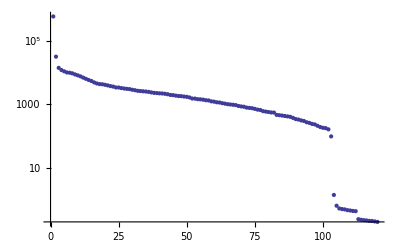

{1196,1196}

$Aborted

```mathematica
Clear[u,s,v]
{u,s,v}=SingularValueDecomposition[m];
Dimensions[s]
ListLogPlot[Diagonal[s],PlotRange->All]
(* Dimensions[u]
ListPlot[Transpose[u][[1]]] *)
Dimensions[v]
i=1;
Monitor[For[i=1, i≤900,, 
p={
ListPlot[Conjugate[Transpose[v][[i]]],ImageSize->500,Joined->True,PlotRange->All],
ListPlot[Transpose[u][[i]],ImageSize->500,Joined->True,PlotRange->All],
ListDensityPlot[Outer[Times,Transpose[u][[i]],Conjugate[Transpose[v][[i]]]],ImageSize->500,PlotRange->All,ColorFunction->"TemperatureMap"]
}
],
EventHandler[p,{"MouseDown" :> i++}]]
```